```mathematica
By Le Chen.
Crated on Sat 30 Apr 2022 07:55:39 AM CDT
```

```mathematica
Integrate[r^(d-1)/(r^2(1+r^2)^(s/2)),{r,0,∞},Assumptions->{s>d-2,d>=3}]
```

(Gamma[-1+d/2] Gamma[1/2 (2-d+s)])/(2 Gamma[s/2])

```mathematica
Solve[z == r^2/(1+r^2),r]
```

{{r→-(√z)/(√(1-z))},{r→(√z)/(√(1-z))}}

```mathematica
FullSimplify[(r^(d-1)/(r^2(1+r^2)^(s/2))/.r->√(z/(1-z)))D[√(z/(1-z)),z]//Expand,Assumptions->{0<z<1,s>d-2,d>=3}]
```

1/2 (1-z)^(1/2 (-d+s)) z^(-2+d/2)

```mathematica
Integrate[1/2 (1-z)^(1/2 (-d+s)) z^(-2+d/2),{z,0,1}]
```

ConditionalExpression[(Gamma[-1+d/2] Gamma[1/2 (2-d+s)])/(2 Gamma[s/2]), Re[d-s]<2&&Re[d]>2]

```mathematica
(Gamma[-1+d/2] Gamma[1/2 (2-d+s)])/(2 Gamma[s/2]) (2 π^(d/2))/Gamma[d/2]
```

(π^(d/2) Gamma[-1+d/2] Gamma[1/2 (2-d+s)])/(Gamma[d/2] Gamma[s/2])

```mathematica
FullSimplify[(π^(d/2) Gamma[-1+d/2] Gamma[1/2 (2-d+s)])/(Gamma[d/2] Gamma[s/2]),Assumptions->{s>d-2,d>=3}]
```

(2 π^(d/2) Gamma[1/2 (2-d+s)])/((-2+d) Gamma[s/2])

```mathematica
(2 π^(d/2) Gamma[1/2 (2-d+s)])/((-2+d) d Gamma[s/2])//TeXForm
```

\frac{2 \pi ^{d/2} \Gamma \left(\frac{1}{2} (-d+s+2)\right)}{(d-2) d \Gamma
   \left(\frac{s}{2}\right)}

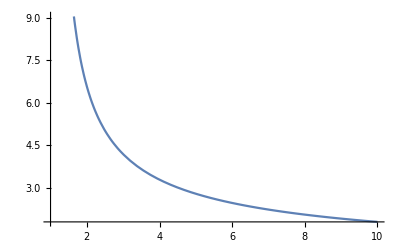

```mathematica
Plot[(2 π^(d/2) Gamma[1/2 (2-d+s)])/((-2+d) d Gamma[s/2])/.d->3,{s,1,10}]
```

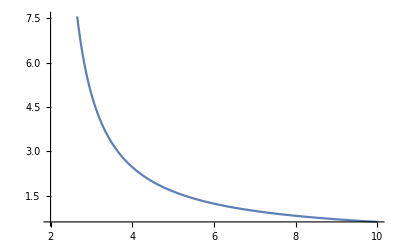

```mathematica
Plot[(2 π^(d/2) Gamma[1/2 (2-d+s)])/((-2+d) d Gamma[s/2])/.d->4,{s,2,10}]
```

```mathematica
Limit[(2 π^(d/2) Gamma[1/2 (2-d+s)])/((-2+d) d Gamma[s/2]),s->∞]
```

$Aborted

```mathematica
Limit[(2 π^(d/2) Gamma[1/2 (2-d+s)])/((-2+d) d Gamma[s/2]),s->∞,Assumptions->{d>=3}]
```

0

```mathematica
D[(2 π^(d/2) Gamma[1/2 (2-d+s)])/((-2+d) d Gamma[s/2]),s]//FullSimplify
```

```mathematica
(π^(d/2) Gamma[1/2 (2-d+s)] (-PolyGamma[0,s/2]+PolyGamma[0,1/2 (2-d+s)]))/((-2+d) d Gamma[s/2])
```

```mathematica
Integrate[Exp[-r z^2] z^(d+s-1),{z,1,∞},Assumptions->r>0]
```

```mathematica
Solve[D[-x √t + Log[t^(d/2+α)],t]==0,t]
```

{{t→(d+2 α)^2/x^2}}

```mathematica
FullSimplify[Exp[-x √t] t^(d/2+α)/.{t->(d+2 α)^2/x^2},Assumptions->{d≥1,α>0,x>0}]
```

ⅇ^(-d-2 α) (x/(d+2 α))^(-d-2 α)

```mathematica
Integrate[t^(α +d/2)(1+r^(2α))Exp[-√t r] r^(d-1),{r,0,∞},Assumptions->{α>0,d≥1,t>0}]
```

t^α Gamma[d]+Gamma[d+2 α]

```mathematica
Integrate[Abs[r-Abs[x]]^a 1/(√(2π))Exp[-x^2/2],{x,-∞,∞},Assumptions->{r>0,a>0}]
```

1/((1+a) √π)2^(-a/2) ⅇ^(-r^2/2) (2^(1/2+a/2) ⅇ^(r^2/2) r^(1+a) HypergeometricPFQ[{1/2,1},{1+a/2,3/2+a/2},-r^2/2]+Gamma[1+a] HypergeometricU[(1+a)/2,1/2,r^2/2]+a Gamma[1+a] HypergeometricU[(1+a)/2,1/2,r^2/2])

```mathematica
Integrate[Abs[r-Abs[x]]^a 1/(√(2π))Exp[-x^2/2],{x,r,∞},Assumptions->{r>0,a>0}]
```

1/(√π)2^(-1-a/2) ⅇ^(-r^2/2) Gamma[1+a] HypergeometricU[(1+a)/2,1/2,r^2/2]

```mathematica
Integrate[Abs[r-Abs[x]]^a 1/(√(2π))Exp[-x^2/2],{x,0,r},Assumptions->{r>0,a>0}]
```

1/((1+a) √(2 π))r^(1+a) HypergeometricPFQ[{1/2,1},{1+a/2,3/2+a/2},-r^2/2]

```mathematica
ϕ (2π)^d 2^(ν-1)/π^(d/2)Gamma[ν+d/2]/.ν->(s-d)/2//FullSimplify
```

2^(1/2 (-2+d+s)) π^(d/2) ϕ Gamma[s/2]

```mathematica
Solve[(ϕ (2π)^d 2^(ν-1)/π^(d/2)Gamma[ν+d/2]/.ν->(s-d)/2)==1,ϕ]//FullSimplify
```

{{ϕ→(2^(1-d/2-s/2) π^(-d/2))/Gamma[s/2]}}

```mathematica
Solve[D[-z^2+Log[z^(d-1)],z]==0,z]
```

{{z→-(√(-1+d))/(√2)},{z→(√(-1+d))/(√2)}}

```mathematica
FullSimplify[Exp[-z^2] z^(d-1)/.z->(√(-1+d))/(√2) ,Assumptions->{d>3}]
```

(-1+d)^(1/2 (-1+d)) (2 ⅇ)^(1/2-d/2)

```mathematica
Integrate[1/((r+z^2)^(s/2)),{z,0,∞},Assumptions->{s>1,r>0}]
```

(√π r^(1/2-s/2) Gamma[1/2 (-1+s)])/(2 Gamma[s/2])

```mathematica
Integrate[1/(r^θ(r+z^2)^(s/2)),{z,0,∞},Assumptions->{s>1,r>0,0<θ<1}]
```

(√π r^(1/2 (1-s-2 θ)) Gamma[1/2 (-1+s)])/(2 Gamma[s/2])

```mathematica
Integrate[Exp[-x^2/2] x^(d-1),{x,2r, ∞},Assumptions->{d>=3,r>0}]
```

2^(-1+d/2) Gamma[d/2,2 r^2]

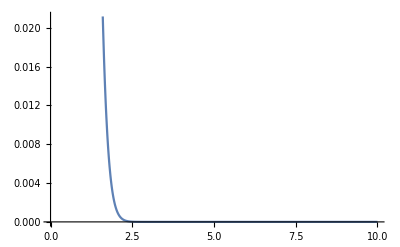

```mathematica
Plot[2^(-1+d/2) Gamma[d/2,2 r^2]/.d->3,{r,0,10}]
```

```mathematica
Limit[2^(-1+d/2) Gamma[d/2,2 r^2],r->0]
```

ConditionalExpression[2^(-1+d/2) Gamma[d/2], d>0]

```mathematica
Integrate[Exp[-x^2/2],{x,2r, ∞},Assumptions->{d>=3,r>0}]
```

√(π/2) Erfc[√2 r]

```mathematica
Integrate[t^(α+d/2)r^(2α +2d-2)Exp[-r^2 -√t r] r^(d-1),{r,0,∞},Assumptions->{t>0,d>=3,α>0}]
```

2^(2-3 d-2 α) t^(d/2+α) Gamma[-2+3 d+2 α] HypergeometricU[-1+(3 d)/2+α,1/2,t/4]

```mathematica
Integrate[(r-x)^2 Exp[-x^2/2] x^2,{x,0,∞},Assumptions->r>0]//Expand//FullSimplify
```

1/2 (3 √(2 π)+r (-8+√(2 π) r))

```mathematica
1/2 (3 √(2 π)+r (-8+√(2 π) r))//Expand//N
```

3.75994-4. r+1.25331 r^2

```mathematica
Integrate[Abs[r-x]^α Exp[-x^2/2],{x,0,∞},Assumptions->{r>0,α>0}]//Expand//FullSimplify
```

1/(1+α)r^(1+α) HypergeometricPFQ[{1/2,1},{1+α/2,3/2+α/2},-r^2/2]+2^(-1-α/2) ⅇ^(-r^2/2) r Gamma[1+α] HypergeometricU[1+α/2,3/2,r^2/2]

```mathematica
Integrate[Abs[r-x]^α Exp[-x^2/2],{x,r,∞},Assumptions->{r>0,α>0}]//FullSimplify
```

2^(-1-α/2) ⅇ^(-r^2/2) r Gamma[1+α] HypergeometricU[1+α/2,3/2,r^2/2]

```mathematica
Integrate[Abs[r-x]^α Exp[-x^2/2],{x,0,r},Assumptions->{r>0,α>0}]//FullSimplify
```

1/(1+α)r^(1+α) HypergeometricPFQ[{1/2,1},{1+α/2,3/2+α/2},-r^2/2]

```mathematica
Integrate[Abs[r-x]^α Exp[-x^2/2],{x,0,2r},Assumptions->{r>0,α>0}]//FullSimplify
```

Integrate[ⅇ^(-x^2/2) Abs[r-x]^α,{x,0,2 r},Assumptions→r>0&&α>0]

```mathematica
Integrate[Abs[r-x]^α Exp[-x^2/2],{x,2r,∞},Assumptions->{r>0,α>0}]//FullSimplify
```

Integrate[ⅇ^(-x^2/2) Abs[r-x]^α,{x,2 r,∞},Assumptions→r>0&&α>0]

```mathematica
Integrate[Exp[-x^2/2],{x,2r,∞},Assumptions->{r>0,α>0}]//FullSimplify
```

√(π/2) Erfc[√2 r]

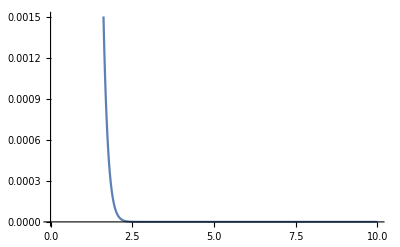

```mathematica
Plot[√(π/2) Erfc[√2 r],{r,0,10}]
```

```mathematica
Integrate[Abs[r-x]^α Exp[-x^2/2]/.r->0,{x,0,∞},Assumptions->{r>0,α>0}]//FullSimplify
```

2^(1/2 (-1+α)) Gamma[(1+α)/2]

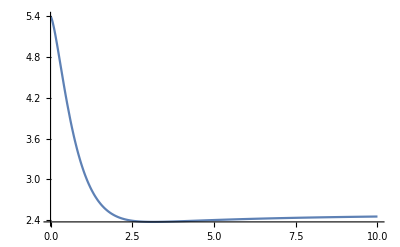

```mathematica
Plot[NIntegrate[Abs[r-x]^α/(1+r^α)Exp[-x^2/2] x^2/.α->3/2,{x,-∞,∞}],{r,0,10},PlotRange->Full]
```

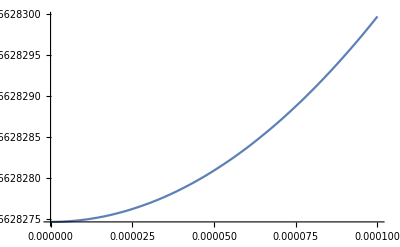

```mathematica
Plot[NIntegrate[Abs[r-x]^α Exp[-x^2/2]/.α->2,{x,-∞,∞}],{r,0,0.0001},PlotRange->Full]
```

```mathematica
Integrate[Abs[r-x]^α Exp[-x^2/2]/.α->2,{x,-∞,∞}]
```

√(2 π) (1+Abs[r]^2)

```mathematica
Integrate[Abs[r-x]^α Exp[-x^2/2]/.α->4,{x,-∞,∞},Assumptions->r>0]
```

√(2 π) (3+6 r^2+r^4)

```mathematica
Integrate[Abs[r-x]^α Exp[-x^2/2]/.α->1/2,{x,-∞,∞},Assumptions->r>0]
```

1/(2 √r)ⅇ^(-r^2/4) π (2 BesselI[1/4,r^2/4]+r^2 BesselI[1/4,r^2/4]+r^2 BesselI[5/4,r^2/4])

```mathematica
Series[Abs[x-r]^α,{r,x,4},Assumptions->α>2]
```

Abs[-r+x]^α

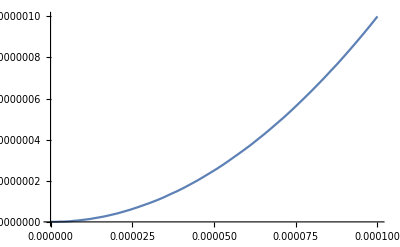

```mathematica
Plot[NIntegrate[Abs[r-x]^α Exp[-x^2/2]/.α->1,{x,-∞,∞}],{r,0,0.0001},PlotRange->Full]
```

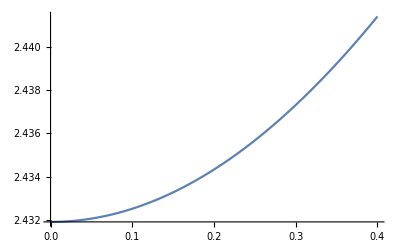

```mathematica
Plot[NIntegrate[Abs[r-x]^α Exp[-x^2/2]/.α->1/20,{x,-∞,∞}],{r,0,0.40},PlotRange->Full]
```

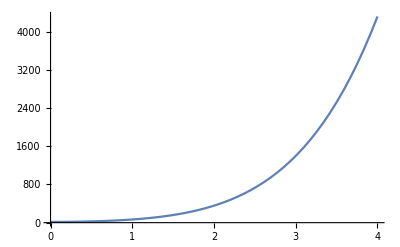

```mathematica
Plot[NIntegrate[Abs[r-x]^α Exp[-x^2/2]/.α->5,{x,-∞,∞}],{r,0,4},PlotRange->Full]
```

```mathematica
Integrate[Abs[r-x]^α Exp[-x^2/2],{x,-∞,∞},Assumptions->{r>0,0<α<2}]
```

2^(-3/2-α/2) ⅇ^(-r^2/2) (2^(3/2+α) ⅇ^(r^2/2) r Gamma[1+α/2] Hypergeometric1F1[1/2-α/2,3/2,-r^2/2]+2^(1+α) ⅇ^(r^2/2) Gamma[(1+α)/2] Hypergeometric1F1[-α/2,1/2,-r^2/2]+√2 r Gamma[1+α] HypergeometricU[1+α/2,3/2,r^2/2])

```mathematica
Integrate[r^α Exp[-x^2/2],{x,-∞,∞},Assumptions->{r>0,0<α<2}]
```

√(2 π) r^α

```mathematica
Integrate[2 x^α Exp[-x^2/2],{x,2,∞},Assumptions->{r>0,0<α<2}]
```

2^(1+α) ExpIntegralE[1/2-α/2,2]

```mathematica
2^(1+α) ExpIntegralE[1/2-α/2,2]-√(2 π) r^α
```

-√(2 π) r^α+2^(1+α) ExpIntegralE[1/2-α/2,2]

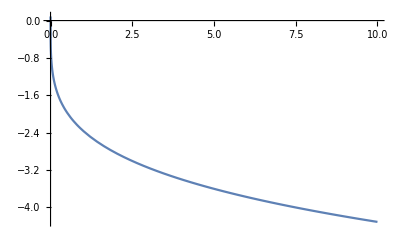

```mathematica
Plot[-√(2 π) r^α+2^(1+α) ExpIntegralE[1/2-α/2,2]/.α->1/4,{r,0,10}]
```

```mathematica
Plot3D[(((r-x)^2)^(α/2))/(1+r^α)/.α->1/2,{r,0,10},{x,-10,10}]
```

-Graphics3D-

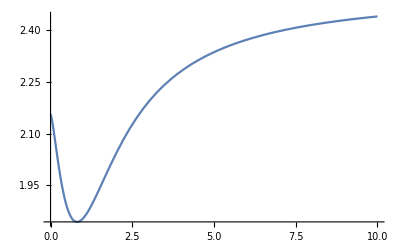

```mathematica
Plot[NIntegrate[Abs[r-x]^α/(1+r^α)Exp[-x^2/2]/.α->3/2,{x,-∞,∞}],{r,0,10},PlotRange->Full]
```

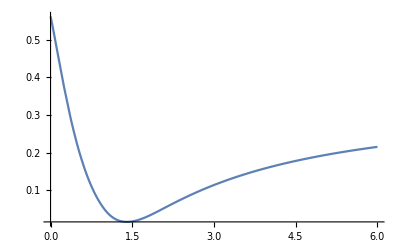

```mathematica
Plot[NIntegrate[Abs[r-x]^α/(1+r^α)Exp[-x^2/2]/.α->3/2,{x,1,2}],{r,0,6},PlotRange->Full]
```

```mathematica
Integrate[Abs[r-x]^α/(1+r^α),{x,1,2},Assumptions->{r>0,α>0}]//FullSimplify
```

Piecewise[{{(-(1-r)^(1+α)+(2-r)^(1+α))/((1+r^α) (1+α)), 0<r≤1}, {((2-r)^(1+α)+(-1+r)^(1+α))/((1+r^α) (1+α)), 1<r<2}, {(-(-2+r)^(1+α)+(-1+r)^(1+α))/((1+r^α) (1+α)), True}}]

```mathematica
FullSimplify[(-(1-r)^(1+α)+(2-r)^(1+α))/((1+r^α) (1+α))/.r->1,Assumptions->α>0]
```

1/(2+2 α)

```mathematica
FullSimplify[((2-r)^(1+α)+(-1+r)^(1+α))/((1+r^α) (1+α))/.r->1,Assumptions->α>0]
```

1/(2+2 α)

```mathematica
FullSimplify[((2-r)^(1+α)+(-1+r)^(1+α))/((1+r^α) (1+α))/.r->2,Assumptions->α>0]
```

1/(1+2^α+α+2^α α)

```mathematica
FullSimplify[(-(-2+r)^(1+α)+(-1+r)^(1+α))/((1+r^α) (1+α))/.r->2,Assumptions->α>0]
```

1/(1+2^α+α+2^α α)

```mathematica
Integrate[Abs[r-x]^α/(1+r^α),{x,0,1},Assumptions->{r>0,α>0}]//FullSimplify
```

Piecewise[{{((1-r)^(1+α)+r^(1+α))/((1+r^α) (1+α)), 0<r<1}, {(-(-1+r)^(1+α)+r^(1+α))/((1+r^α) (1+α)), True}}]

```mathematica
Integrate[(((r-x)^2)^(α/2))/(1+r^α),{x,1,2},Assumptions->{r>0,α>0}]//FullSimplify
```

```mathematica
((2-r) Abs[-2+r]^α+(-1+r) Abs[-1+r]^α)/((1+r^α) (1+α))
```

```mathematica
Integrate[(((r-x)^2)^(α/2))/(1+r^α),{x,1,2},Assumptions->{r>0,α>0}]
```

(-((-2+r) Abs[-2+r]^α)+(-1+r) Abs[-1+r]^α)/((1+r^α) (1+α))

```mathematica
Integrate[(((r-x)^2)^(α/2))/(1+r^α),{x,1,2},Assumptions->{r>2,α>0}]
```

(-(-2+r)^(1+α)+(-1+r)^(1+α))/((1+r^α) (1+α))

```mathematica
(-(-2+r)^(1+α)+(-1+r)^(1+α))/((1+r^α) (1+α))
```

```mathematica
Integrate[(((r-x)^2)^(α/2))/(1+r^α),{x,1,2},Assumptions->{2>r>1,α>0}]
```

((2-r)^(1+α)+(-1+r)^(1+α))/((1+r^α) (1+α))

```mathematica
Integrate[((r-x)^2)^(α/2) /(1+r^α),{x,1,2},Assumptions->{r<1,α>0}]
```

(-(1-r)^(1+α)+(2-r)^(1+α))/((1+r^α) (1+α))

```mathematica
Integrate[(((r-x)^2)^(α/2))/(1+r^α),{x,1,2},Assumptions->{2>r>1,α>0}]
```

((2-r)^(1+α)+(-1+r)^(1+α))/((1+r^α) (1+α))

```mathematica
D[((2-r)^(1+α)+(-1+r)^(1+α))/(1+r^α),r]//FullSimplify
```

-(((2-r)^(1+α)+(-1+r)^(1+α)) r^(-1+α) α+((2-r)^α-(-1+r)^α) (1+r^α) (1+α))/((1+r^α)^2)

```mathematica
Solve[((2-r)^(1+α)+(-1+r)^(1+α)) r^(-1+α) α+((2-r)^α-(-1+r)^α) (1+r^α) (1+α)==0,r]
```

$Aborted

```mathematica
Solve[(2-r)==(-1+r),r]
```

{{r→3/2}}

```mathematica
((2-r)^(1+α)+(-1+r)^(1+α))/((1+r^α) (1+α))/.r->3/2//FullSimplify
```

1/((2^α+3^α) (1+α))

```mathematica
Solve[D[(2-r)^(1+α)+(-1+r)^(1+α),r]==0,r,Assumptions->{α>0,r>0}]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[-(2-r)^α (1+α)+(-1+r)^α (1+α)==0,r,Assumptions→{α>0,r>0}]

```mathematica
Integrate[(((r-x)^2)^(α/2))/(1+r^α),{x,1,2},Assumptions->{r>2,α>0}]
```

(-(-2+r)^(1+α)+(-1+r)^(1+α))/((1+r^α) (1+α))

```mathematica
Integrate[(((r-x)^2)^(α/2))/(1+r^α),{x,1,2},Assumptions->{r>0,α>0}]//FullSimplify
```

(-((-2+r) Abs[-2+r]^α)+(-1+r) Abs[-1+r]^α)/((1+r^α) (1+α))

```mathematica
((r-2) Abs[-2+r]^α+(-1+r) Abs[-1+r]^α)/((1+r^α) (1+α))
```

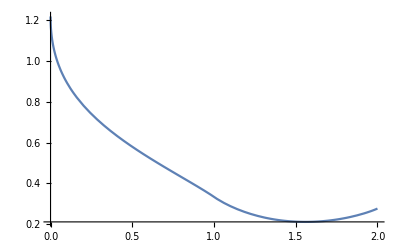

```mathematica
Plot[(-((-2+r) Abs[-2+r]^α)+(-1+r) Abs[-1+r]^α)/((1+r^α) (1+α))/.α->1/2,{r,0,2}]
```

```mathematica
Plot[NIntegrate[(r-x)^a/(1+r^a)/.a->1/2,{x,1,2}],{r,2,10}]
```

```mathematica
.
```

```mathematica
(-(-2+r)^(1+α)+(-1+r)^(1+α))/((1+r^α) (1+α))/.α->1/2
```

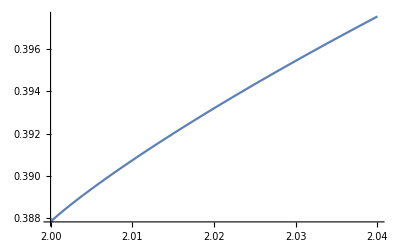

```mathematica
Plot[(-(-2+r)^(1+α)+(-1+r)^(1+α))/((1+r^α) (1+α))/.α->1/5,{r,2,2.04},PlotRange->Full]
```

```mathematica
D[(-(-2+r)^(1+α)+(-1+r)^(1+α))/(1+r^α),r]//FullSimplify
```

```mathematica
(-(-2+r)^(1+α)+(-1+r)^(1+α)) r^(-1+α) α+((-2+r)^α-(-1+r)^α) (1+r^α) (1+α)
```

```mathematica
FullSimplify[(-(-2+r)^(1+α)+(-1+r)^(1+α)) r^(-1+α) α+((-2+r)^α-(-1+r)^α) (1+r^α) (1+α),Assumptions->{α>0,r>2}]
```

(-(-2+r)^(1+α)+(-1+r)^(1+α)) r^(-1+α) α+((-2+r)^α-(-1+r)^α) (1+r^α) (1+α)

```mathematica
Integrate[r^-α Log[r],{r,0,t},Assumptions->t>0]
```

ConditionalExpression[-(t^(1-α) (1+(-1+α) Log[t]))/(-1+α)^2, Re[α]<1]

```mathematica
Integrate[Log[r],{r,0,t},Assumptions->t>0]
```

t (-1+Log[t])

```mathematica
Solve[D[-r z^2+Log[z^(d-1)],z]==0,z]
```

{{z→-(√(-1+d))/(√2 √r)},{z→(√(-1+d))/(√2 √r)}}

```mathematica
FullSimplify[Exp[-r z^2] z^(d-1)/.z->(√(-1+d))/(√2 √r),Assumptions->{d≥3, r>0}]
```

(2 ⅇ)^(1/2-d/2) ((-1+d)/r)^(1/2 (-1+d))

```mathematica
Integrate[Exp[-r z^2] z^(d-1)/((1+z^2)^(s/2)),{z,0,∞},Assumptions->{d≥3,s>0,r>0}]
```

1/2 Gamma[d/2] HypergeometricU[d/2,1/2 (2+d-s),r]

```mathematica
FullSimplify[Series[1/2 Gamma[d/2] HypergeometricU[d/2,1/2 (2+d-s),r],{r,0,0}],Assumptions->{0<s<d}]
```

r^(1/2 (-d+s)) (1/2 Gamma[(d-s)/2]+O[r]^1)+((Gamma[d/2] Gamma[1/2 (-d+s)])/(2 Gamma[s/2])+O[r]^1)

```mathematica
FullSimplify[Series[1/2 Gamma[d/2] HypergeometricU[d/2,1/2 (2+d-s),r],{r,0,0}],Assumptions->{s>d≥3}]
```

r^(1/2 (-d+s)) (1/2 Gamma[(d-s)/2]+O[r]^1)+((Gamma[d/2] Gamma[1/2 (-d+s)])/(2 Gamma[s/2])+O[r]^1)

```mathematica
FullSimplify[Series[1/2 Gamma[d/2] HypergeometricU[d/2,1/2 (2+d-s),r],{r,0,0}],Assumptions->{s==d}]
```

ComplexInfinity+O[r]^1

```mathematica
Solve[1/2 (2+d-s)==2,s]
Solve[1/2 (2+d-s)==1,s]
Solve[1/2 (2+d-s)==0,s]
```

{{s→-2+d}}

{{s→d}}

{{s→2+d}}

```mathematica
Integrate[Exp[-r u]/(1+u)^(s/2)u^(d/2-1)1/2,{u,0,∞},Assumptions->{r>0,d>0}]
```

1/2 Gamma[d/2] HypergeometricU[d/2,1/2 (2+d-s),r]

```mathematica
Five cases
```

```mathematica
13.2-18
```

```mathematica
b= (2+d-s)/2;
a= d/2;
Gamma[b-1]/Gamma[a] r^(1-b) + Gamma[1-b]/Gamma[a-b+1]+  z^(2-b)//FullSimplify
```

z^(1/2 (2-d+s))+(r^(1/2 (-d+s)) Gamma[(d-s)/2])/Gamma[d/2]+Gamma[1/2 (-d+s)]/Gamma[s/2]

```mathematica
π^(d/2)Integrate[(Gamma[b-1]/Gamma[a] r^(1-b) + Gamma[1-b]/Gamma[a-b+1])r^(-2α),{r,0,t},Assumptions->{0<α<1/2,t>0,d≥3,d>s>d-2,d+4 α<2+s}]//FullSimplify//Expand
Integrate[r^(2-b)r^(-2α),{r,0,t},Assumptions->{0<α<1/2,t>0,d≥3,d>s>d-2,d+4 α<2+s}]//FullSimplify//Expand
```

```mathematica
-(2 π^(d/2) t^(1+1/2 (-d+s)-2 α) Gamma[(d-s)/2])/((-2+d-s+4 α) Gamma[d/2])-(π^(d/2) t^(1-2 α) Gamma[1/2 (-d+s)])/((-1+2 α) Gamma[s/2])
```

-(2 t^(1/2 (4-d+s-4 α)))/(-4+d-s+4 α)

```mathematica
-(2 t^(1/2 (4-d+s-4 α)))/(-4+d-s+4 α)
```

```mathematica
z^(1/2 (2-d+s))+(r^(1/2 (-d+s)) Gamma[(d-s)/2])/Gamma[d/2]+Gamma[1/2 (-d+s)]/Gamma[s/2]//TeXForm
```

\frac{r^{\frac{s-d}{2}} \Gamma
   \left(\frac{d-s}{2}\right)}{\
   Gamma
   \left(\frac{d}{2}\right)}+z^{
   \frac{1}{2}
   (-d+s+2)}+\frac{\Gamma
   \left(\frac{s-d}{2}\right)}{\
   Gamma
   \left(\frac{s}{2}\right)}

```mathematica
13.2-19
```

```mathematica
b= (2+d-s)/2;
a= d/2;
-1/Gamma[a](Log[r]+PolyGamma[a]+2γ)+  z Log[z]//FullSimplify
```

z Log[z]-(2 γ+Log[r]+PolyGamma[0,d/2])/Gamma[d/2]

```mathematica
π^(d/2)Integrate[(-1/Gamma[a](Log[r]+ψ[a]+2γ))r^(-2α),{r,0,t},Assumptions->{0<α<1/2,t>0,d≥3,d>s>d-2,d+4 α<2+s}]//FullSimplify
```

(π^(d/2) t^(1-2 α) (1-2 γ+4 α γ+(-1+2 α) Log[t]+(-1+2 α) ψ[d/2]))/((1-2 α)^2 Gamma[d/2])

```mathematica
(π^(d/2) t^(1-2 α) (1-2 γ+4 α γ+(-1+2 α) Log[t]+(-1+2 α) ψ[d/2]))/((1-2 α)^2 Gamma[d/2])//TeXForm
```

\frac{\pi ^{d/2} t^{1-2 \alpha
   } \left(4 \alpha  \gamma -2
   \gamma +(2 \alpha -1) \psi
   \left(\frac{d}{2}\right)+(2
   \alpha -1) \log
   (t)+1\right)}{(1-2 \alpha
   )^2 \Gamma
   \left(\frac{d}{2}\right)}

```mathematica
Integrate[r Log[r],{r,0,t},Assumptions->{0<α<1/2,t>0,d≥3,d>s>d-2,d+4 α<2+s}]//FullSimplify
```

1/4 t^2 (-1+2 Log[t])

```mathematica
13.2-20
```

```mathematica
b= (2+d-s)/2;
a= d/2;
Gamma[1-b]/Gamma[a-b+1]+  z^(1-b)//FullSimplify
```

z^(1/2 (-d+s))+Gamma[1/2 (-d+s)]/Gamma[s/2]

```mathematica
π^(d/2)Integrate[Gamma[1/2 (-d+s)]/Gamma[s/2] r^(-2α),{r,0,t},Assumptions->{0<α<1/2,t>0,d≥3,d>s>d-2,d+4 α<2+s}]//FullSimplify
```

(π^(d/2) t^(1-2 α) Gamma[1/2 (-d+s)])/((1-2 α) Gamma[s/2])

```mathematica
π^(d/2)Integrate[r^(1/2 (-d+s))r^(-2α),{r,0,t},Assumptions->{0<α<1/2,t>0,d≥3,d>s>d-2,d+4 α<2+s}]//FullSimplify
```

-(2 π^(d/2) t^(1/2 (2-d+s-4 α)))/(-2+d-s+4 α)

```mathematica
13.2-21
```

```mathematica
b= (2+d-s)/2;
a= d/2;
1/Gamma[a+1]+  z Log[z]//FullSimplify
```

1/Gamma[1+d/2]+z Log[z]

```mathematica
π^(d/2)Integrate[1/Gamma[a+1] r^(-2α),{r,0,t},Assumptions->{0<α<1/2,t>0,d≥3,d>s>d-2,d+4 α<2+s}]//FullSimplify
```

(π^(d/2) t^(1-2 α))/((1-2 α) Gamma[1+d/2])

```mathematica
π^(d/2)Integrate[r Log[r] r^(-2α),{r,0,t},Assumptions->{0<α<1/2,t>0,d≥3,d>s>d-2,d+4 α<2+s}]//FullSimplify
```

-(π^(d/2) t^(2-2 α) (1+2 (-1+α) Log[t]))/(4 (-1+α)^2)

```mathematica
13.2-22
```

```mathematica
b= (2+d-s)/2;
a= d/2;
1/Gamma[a+1]+  z //FullSimplify
```

```mathematica
Solve[(s-d-2)/4==1/2,s]
```

{{s→4+d}}

```mathematica
π^(d/2)Integrate[1/Gamma[a+1] r^(-2α),{r,0,t},Assumptions->{0<α<1/2,t>0,d≥3,d>s>d-2,d+4 α<2+s}]//FullSimplify
```

(π^(d/2) t^(1-2 α))/((1-2 α) Gamma[1+d/2])

```mathematica
Tessitore, p. 279
```

```mathematica
Integrate[(4π s)^(-d/2)Exp[-x^2/(4s)],{s,0,∞},Assumptions->x>0]
```

ConditionalExpression[1/4 π^(-d/2) x^(2-d) Gamma[-1+d/2], Re[d]>2]

```mathematica
(Gamma[d/2-1] 2^(d/2-2))/(2 π)^d
```

```mathematica
π^(-d/2)2^-α Gamma[(d-α)/2]/Gamma[α/2]/.α-> d-2//FullSimplify
```

(2^(2-d) π^(-d/2))/Gamma[-1+d/2]

```mathematica
(Gamma[d/2-1] 2^(d/2-2))/(2 π)^d(2^(2-d) π^(-d/2))/Gamma[-1+d/2]
```

(2 π)^(-3 d/2)

```mathematica
Gamma[d/2-1]/(4 π^(d/2))(2^(2-d) π^(-d/2))/Gamma[-1+d/2]
```

(2 π)^-d

```mathematica
(Gamma[d/2-1] 2^(d/2-2))/(2π)^d(2^(2-d) π^(-d/2))/Gamma[-1+d/2]
```

(2 π)^(-3 d/2)

```mathematica
(Gamma[d/2-1] (2π)^(d/2))/(4 π^(d/2))(2π)^-d(2^(2-d) π^(-d/2))/Gamma[-1+d/2]
```

(2 π)^(-3 d/2)

```mathematica
(2π)^(3/2)//N
```

15.7496

```mathematica
d
```

d

```mathematica
Solve[256 == (2 π)^(d / 2),d]
```

{{d→ConditionalExpression[(2 (2 ⅈ π C[1]+Log[256]))/Log[2 π], C[1]∈ℤ]}}

```mathematica
(2 (Log[256]))/Log[2 π]//N
```

6.03433

```mathematica
(2 (Log[256]))/Log[2 π]//FullSimplify
```

(16 Log[2])/Log[2 π]

```mathematica
Integrate[Exp[-r^2/(2t)] r^(-α+d-1),{r,0,∞},Assumptions->{t>0,0<α<d}]
```

2^(1/2 (-2+d-α)) t^((d-α)/2) Gamma[(d-α)/2]

```mathematica
2^(1/2 (-2+d-α)) t^((d-α)/2) Gamma[(d-α)/2] (2 π^(d/2))/Gamma[d/2] (2π t)^(-d/2)//FullSimplify
```

(2^(-α/2) t^(-α/2) Gamma[(d-α)/2])/Gamma[d/2]

```mathematica
Integrate[1/2 Exp[-ⅈ x y],{x,-1,1}]
```

Sin[y]/y

```mathematica
1/(√(2π))InverseFourierTransform[Sin[y]^2/y^2,y,x]//FullSimplify
```

1/8 ((-2+x) Sign[-2+x]-2 x Sign[x]+(2+x) Sign[2+x])

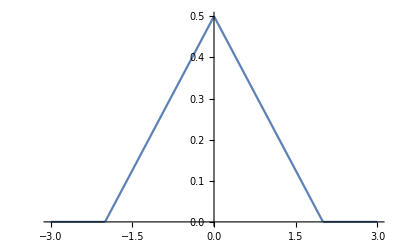

```mathematica
Plot[1/8 ((-2+x) Sign[-2+x]-2 x Sign[x]+(2+x) Sign[2+x]),{x,-3,3}]
```

```mathematica
InverseFourierTransform[Abs[Sin[x]/x],x,y]
```

$Aborted

```mathematica
Integrate[Tan[π^2 t]/t,{t,-1/(2π),1/(2π)}]
```

∫_(-1/(2 π))^(1/(2 π)) Tan[π^2 t]/t ⅆt

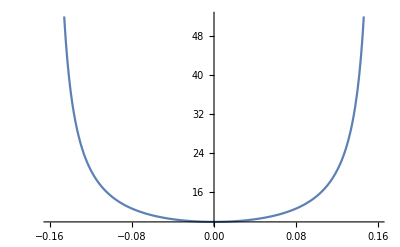

```mathematica
Plot[Tan[π^2 t]/t,{t,-1/(2π),1/(2π)}]
```

```mathematica
NIntegrate[Tan[π^2 t]/t,{t,-1/(2π),1/(2π)}]
```

45.3553

```mathematica
Integrate[Exp[-r x^2] r^(-2α),{r,0,∞},Assumptions->{x>0,α<1/2}]
```

x^(-2+4 α) Gamma[1-2 α]

```mathematica
Integrate[Exp[-r u] r^(-2α) (1+u)^(-s/2)u^(d/2-1),{r,0,∞},Assumptions->{u>0,d≥3,0<α<1/2}]
```

u^(-2+d/2+2 α) (1+u)^(-s/2) Gamma[1-2 α]

```mathematica
Integrate[u^(-2+d/2+2 α) (1+u)^(-s/2) Gamma[1-2 α],{u,0,∞},Assumptions->{0<α<1/2,d≥3,s>d-2}]
```

ConditionalExpression[1/Gamma[s/2]Gamma[1/2 (2-d+s-4 α)] Gamma[1-2 α] Gamma[-1+d/2+2 α], d+4 α<2+s]

```mathematica
Integrate[Exp[-r x^2],{r,1,∞},Assumptions->{x>0,α<1/2}]
```

(ⅇ^(-x^2))/x^2

```mathematica
Integrate[Exp[-r x^2],{r,0,1},Assumptions->{x>0,α<1/2}]
```

(1-ⅇ^(-x^2))/x^2

```mathematica
Integrate[Exp[-r x^2] r^(-2α),{r,0,t},Assumptions->{x>0,α<1/2,t>0}]
```

x^(-2+4 α) (Gamma[1-2 α]-Gamma[1-2 α,t x^2])

```mathematica
D[Exp[-r x^2] r^(-2α),α]
```

-2 ⅇ^(-r x^2) r^(-2 α) Log[r]

```mathematica
Integrate[D[Exp[-r x^2] r^(-2α),α],{r,0,t},Assumptions->{x>0,α<1/2,t>0}]
```

2 x^(-2+4 α) (Gamma[1-2 α,t x^2] Log[t]+MeijerG[{{},{1,1}},{{0,0,1-2 α},{}},t x^2]+Gamma[1-2 α] (2 Log[x]-PolyGamma[0,1-2 α]))

```mathematica
Integrate[Exp[-r x^2],{r,t,∞},Assumptions->{x>0,α<1/2,t>0}]
```

(ⅇ^(-t x^2))/x^2

```mathematica
Solve[D[-t r -Log[r^2],r]==0,r]
```

{{r→-2/t}}

```mathematica
Solve[z==r^2/(1+r^2),r]
```

{{r→-(√z)/(√(1-z))},{r→(√z)/(√(1-z))}}

```mathematica
FullSimplify[(r^(d-1)/(r^(2(1-α))(1+r^2)^(s/2)) /.r->(√z)/(√(1-z)) )D[(√z)/(√(1-z)),z],Assumptions->{z>0,d>=3, α>0}]
```

((-1+1/z)^(-d/2-α) (1/(1-z))^(-s/2))/(2 z^2)

```mathematica
Integrate[((-1+1/z)^(-d/2-α) (1/(1-z))^(-s/2))/(2 z^2),{z,0,1},Assumptions->{s>d-2, d>=3,0<α<1/2}]
```

ConditionalExpression[(Gamma[1/2 (2-d+s-2 α)] Gamma[-1+d/2+α])/(2 Gamma[s/2]), d+2 α<2+s]

```mathematica
1/2 (1-z)^(s/2) (1-z)^(-d/2-α) z^(-2-d/2-α)
```

1/2 (1-z)^(-d/2+s/2-α) z^(-2-d/2-α)

```mathematica
Integrate[(1-z)^(-d/2+s/2-α) z^(-2-d/2-α),{z,0,1},Assumptions->{s>d-2, d>=3}]
```

ConditionalExpression[(Gamma[1/2 (2-d+s-2 α)] Gamma[-1-d/2-α])/Gamma[-d+s/2-2 α], Re[α]<-5/2&&d+2 Re[α]<-2]

```mathematica
Integrate[r^(d-1)/(r^(2(1-α))(1+r^2)^(s/2)),{r,0,∞},Assumptions->{s>d-2, d>=3,0<α<1/2}]
```

ConditionalExpression[(Gamma[1/2 (2-d+s-2 α)] Gamma[-1+d/2+α])/(2 Gamma[s/2]), d+2 α<2+s]

```mathematica
Integrate[(1-z)^(-d/2+s/2-α) z^(-2+d/2+α),{z,0,1},Assumptions->{s>d-2, d>=3,α>0}]
```

ConditionalExpression[(Gamma[1/2 (2-d+s-2 α)] Gamma[-1+d/2+α])/Gamma[s/2], d+2 α<2+s]

```mathematica
((Gamma[1/2 (2-d+s-2 α)] Gamma[-1+d/2+α])/(2 Gamma[s/2])) (2 π^(d/2))/Gamma[d/2] (2π)^-d//FullSimplify
```

(2^-d π^(-d/2) Gamma[1/2 (2-d+s-2 α)] Gamma[-1+d/2+α])/(Gamma[d/2] Gamma[s/2])

```mathematica
(2^-d π^(-d/2) Gamma[1/2 (2-d+s-2 α)] Gamma[-1+d/2+α])/(Gamma[d/2] Gamma[s/2])/.α->0//FullSimplify
```

(2^(1-d) π^(-d/2) Gamma[1/2 (2-d+s)])/((-2+d) Gamma[s/2])

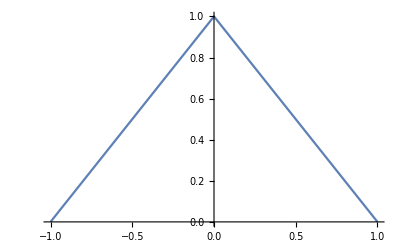

```mathematica
Plot[1-Abs[x],{x,-1,1}]
```

```mathematica
Integrate[2 √(1-x)Cos[x y],{x,0,1},Assumptions->y>0]
Exp[ⅈ x y] = Cos[x y] + ⅈ Sin[x y]
```

1/y^(3/2)√(2 π) (-Cos[y] FresnelS[√(2/π) √y]+FresnelC[√(2/π) √y] Sin[y])

Set::write: Tag Exp in Exp[ⅈ x y] is Protected.

Cos[x y]+ⅈ Sin[x y]

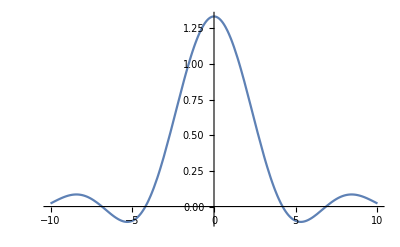

```mathematica
Plot[1/y^(3/2)√(2 π) (-Cos[y] FresnelS[√(2/π) √y]+FresnelC[√(2/π) √y] Sin[y]),{y,-10,10}]
```

```mathematica
Integrate[2 √(1-x)Cos[x y],{x,0,1}]
```

-(ⅇ^(-ⅈ y) √π (-ⅇ^(2 ⅈ y) Erf[√(ⅈ y)]+Erfi[√(ⅈ y)]))/(2 (ⅈ y)^(3/2))

```mathematica
Integrate[Exp[-(x-y)^2 +Abs[x]^a-Abs[y]^a]/.a->3/2,{y,-∞,∞},Assumptions->x>0]
```

Integrate[ⅇ^(-(x-y)^2+Abs[x]^(3/2)-Abs[y]^(3/2)),{y,-∞,∞},Assumptions→x>0]

```mathematica
Integrate[Exp[-(x-y)^2 +Abs[x]^a-Abs[y]^a]/.a->3/2,{y,-2x,2x},Assumptions->{x>0}]
```

Integrate[ⅇ^(-(x-y)^2+Abs[x]^(3/2)-Abs[y]^(3/2)),{y,-2 x,2 x},Assumptions→{x>0}]

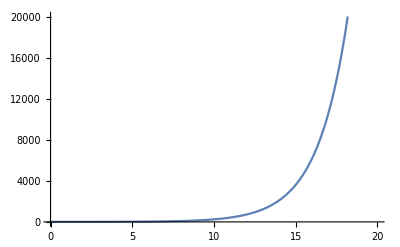

```mathematica
Plot[NIntegrate[Exp[-(x-y)^2 +Abs[x]^a-Abs[y]^a]/.a->3/2,{y,-∞,∞}],{x,0,20}]
```

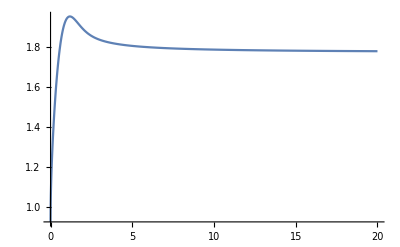

```mathematica
Plot[NIntegrate[Exp[-(x-y)^2 +Abs[x]^a-Abs[y]^a]/.a->1/2,{y,-∞,∞}],{x,0,20},PlotRange->Full]
```

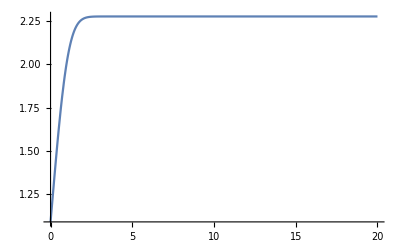

```mathematica
Plot[NIntegrate[Exp[-(x-y)^2 +Abs[x]^a-Abs[y]^a]/.a->1,{y,-∞,∞}],{x,0,20},PlotRange->Full]
```

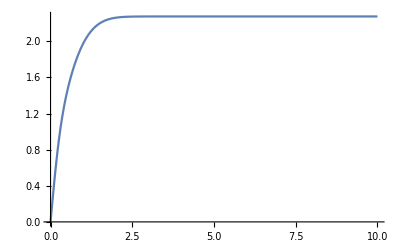

```mathematica
Plot[NIntegrate[Exp[-(x-y)^2 +Abs[x]^a-Abs[y]^a]/.a->1,{y,-2x,2x}],{x,0,10},PlotRange->Full]
```

```mathematica
Plot[NIntegrate[Exp[-(x-y)^2 +Abs[x]^a-Abs[y]^a]/.a->1.8,{y,-10,10}],{x,0,20},PlotRange->Full]
```

-Graphics-

```mathematica
Plot3D[(-(x-y)^2 +Abs[x]^a-Abs[y]^a)/.a->1.1,{x,-10,10},{y,-18,18}]
```

-Graphics3D-

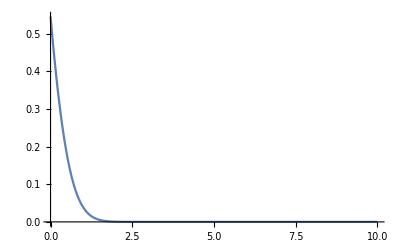

```mathematica
Plot[NIntegrate[Exp[-(x-y)^2 +Abs[x]^a-Abs[y]^a]/.a->1,{y,2x,∞}],{x,0,10},PlotRange->Full]
```

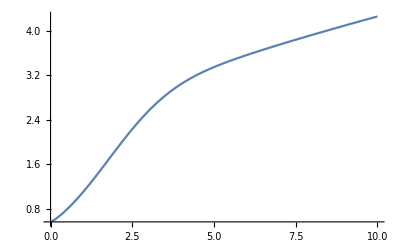

```mathematica
Plot[NIntegrate[Exp[-(x-y)^2 +Abs[x]^a-Abs[y]^a]/.a->1.2,{y,0.5x, 2x,∞}],{x,0,10},PlotRange->Full]
```

```mathematica
D[(x-y)^2+ y^b,y]
Solve[%==0/.b->3/2,y]
```

-2 (x-y)+b y^(-1+b)

{{y→1/32 (9+32 x-3 √(9+64 x))},{y→1/32 (9+32 x+3 √(9+64 x))}}

```mathematica
(x-y)^2+ y^(3/2) -x^(3/2)/.y->1/32 (9+32 x+3 √(9+64 x))//FullSimplify
Limit[%/x^(3/2),x->∞]
```

1/512 (81+288 x-512 x^(3/2)+27 √(9+64 x)+2 √2 (9+32 x+3 √(9+64 x))^(3/2))

0

```mathematica
Limit[ 1/x^(3/2)1/512 (9+32 x+3 √(9+64 x))(9+2 √(64 x+6 (3+√(9+64 x)))),x->∞]
```

1

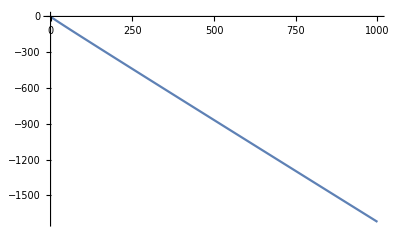

```mathematica
Plot[-1/512 (81+288 x-512 x^(3/2)+27 √(9+64 x)+2 √2 (9+32 x+3 √(9+64 x))^(3/2)),{x,0,1000}]
```

```mathematica
D[(x-y)^2+ y^b,y]
Solve[%==0/.b->1,y]
(x-y)^2+ y^b -x^b/.b->1/.{y->1/2 (-1+2 x)}//FullSimplify
```

-2 (x-y)+b y^(-1+b)

{{y→1/2 (-1+2 x)}}

-1/4

```mathematica
D[(x-y)^2+ y^b,y]
Solve[%==0/.b->2/3,y]
(x-y)^2+ y^b -x^b/.b->2/3/.{y->1/2 (-1+2 x)}//FullSimplify
```

-2 (x-y)+b y^(-1+b)

{{y→(3 x)/4+1/12 √(9 x^2+(16 2^(1/3))/((27 x^2+√(-256+729 x^4))^(1/3))+2 2^(2/3) (27 x^2+√(-256+729 x^4))^(1/3))-1/2 √(x^2/2-(4 2^(1/3))/(9 (27 x^2+√(-256+729 x^4))^(1/3))-((27 x^2+√(-256+729 x^4))^(1/3))/(9 2^(1/3))-(3 x^3)/(2 √(9 x^2+(16 2^(1/3))/((27 x^2+√(-256+729 x^4))^(1/3))+2 2^(2/3) (27 x^2+√(-256+729 x^4))^(1/3))))},{y→(3 x)/4+1/12 √(9 x^2+(16 2^(1/3))/((27 x^2+√(-256+729 x^4))^(1/3))+2 2^(2/3) (27 x^2+√(-256+729 x^4))^(1/3))+1/2 √(x^2/2-(4 2^(1/3))/(9 (27 x^2+√(-256+729 x^4))^(1/3))-((27 x^2+√(-256+729 x^4))^(1/3))/(9 2^(1/3))-(3 x^3)/(2 √(9 x^2+(16 2^(1/3))/((27 x^2+√(-256+729 x^4))^(1/3))+2 2^(2/3) (27 x^2+√(-256+729 x^4))^(1/3))))},{y→(3 x)/4-1/12 √(9 x^2+(16 2^(1/3))/((27 x^2+√(-256+729 x^4))^(1/3))+2 2^(2/3) (27 x^2+√(-256+729 x^4))^(1/3))-1/2 √(x^2/2-(4 2^(1/3))/(9 (27 x^2+√(-256+729 x^4))^(1/3))-((27 x^2+√(-256+729 x^4))^(1/3))/(9 2^(1/3))+(3 x^3)/(2 √(9 x^2+(16 2^(1/3))/((27 x^2+√(-256+729 x^4))^(1/3))+2 2^(2/3) (27 x^2+√(-256+729 x^4))^(1/3))))},{y→(3 x)/4-1/12 √(9 x^2+(16 2^(1/3))/((27 x^2+√(-256+729 x^4))^(1/3))+2 2^(2/3) (27 x^2+√(-256+729 x^4))^(1/3))+1/2 √(x^2/2-(4 2^(1/3))/(9 (27 x^2+√(-256+729 x^4))^(1/3))-((27 x^2+√(-256+729 x^4))^(1/3))/(9 2^(1/3))+(3 x^3)/(2 √(9 x^2+(16 2^(1/3))/((27 x^2+√(-256+729 x^4))^(1/3))+2 2^(2/3) (27 x^2+√(-256+729 x^4))^(1/3))))}}

1/4+(-1/2+x)^(2/3)-x^(2/3)

```mathematica
D[(x-y)^2+ y^b,y]
%/.b->3/2
Solve[%==0,y]
```

-2 (x-y)+b y^(-1+b)

-2 (x-y)+(3 √y)/2

{{y→1/32 (9+32 x-3 √(9+64 x))},{y→1/32 (9+32 x+3 √(9+64 x))}}

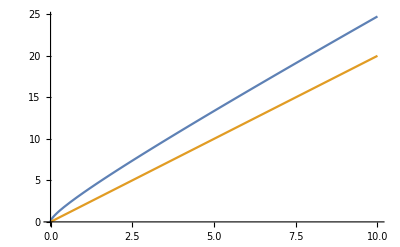

```mathematica
Plot[{2y + 3(√y)/2,2y},{y,0,10}]
```

```mathematica
D[(x-y)^2+ y^b,y]
%/.b->1/2
```

-2 (x-y)+b y^(-1+b)

-2 (x-y)+1/(2 √y)

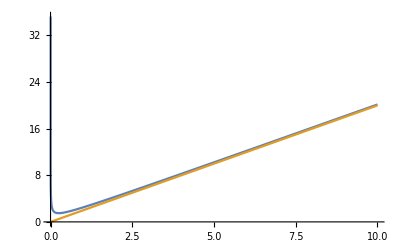

```mathematica
Plot[{2y + 1/(2 √y),2y},{y,0,10}]
```

```mathematica
Solve[y+√y==x,y]
```

{{y→1/2 (1+2 x-√(1+4 x))},{y→1/2 (1+2 x+√(1+4 x))}}

```mathematica
Limit[(-x + x^(3/2)-(x-√x)^(3/2))/x,x->∞]
```

1/2

```mathematica
FullSimplify[-(b/2)^2 y^(2(b-1)) + (y + b/2 y^(b-1))^b-y^b,Assumptions->{y>0,1<b≤2}]
```

-y^b-1/4 b^2 y^(-2+2 b)+(y+1/2 b y^(-1+b))^b

```mathematica
FullSimplify[-((b-1)/2)^2 y^(2(b-1)) + y^b + ((b-1)/2)^b y^(b(b-1))-y^b,Assumptions->{y>0,1<b≤2}]
%/.b->3/2//FullSimplify
```

```mathematica
2^-b (-1+b)^b-1/4 (-1+b)^2 y^(-2+2 b - (-1+b) b)
```

1/16 (2 y^(3/4)-y)

```mathematica
FullSimplify[(-1+b) b < -2 + 2b,Assumptions->1<b<2]
```

True

```mathematica
FullSimplify[-2+2 b - (-1+b) b,Assumptions->1<b<2]
```

-(-2+b) (-1+b)

```mathematica
FullSimplify[((2^-b (-1+b)^b)/(1/4 (-1+b)^2))^(1/(-(-2+b) (-1+b))),Assumptions->1<b<2]
```

2^(1/(-1+b)) (-1+b)^(1/(1-b))

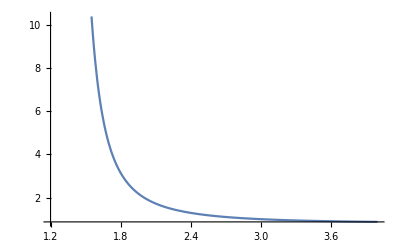

```mathematica
Plot[2^(1/(-1+b)) (-1+b)^(1/(1-b)),{b,1.2,4}]
```

```mathematica
Limit[2^(1/(-1+b)) (-1+b)^(1/(1-b)),b->∞]
```

1

```mathematica
Integrate[Exp[1/16 (4 y^(3/4)-y)],{y,x-1,x+1},Assumptions->x>1]
```

Integrate[ⅇ^(1/16 (4 y^(3/4)-y)),{y,-1+x,1+x},Assumptions→x>1]

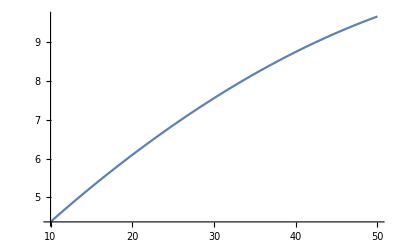

```mathematica
Plot[NIntegrate[Exp[1/16 (4 y^(3/4)-y)],{y,x-1,x+1}],{x,10,50}]
```

```mathematica
FullSimplify[D[2^-b (-1+b)^b y^((-1+b) b)-1/4 (-1+b)^2 y^(-2+2 b),y],Assumptions->1<b<2]
FullSimplify[Solve[%==0,y],Assumptions->1<b<2]
```

-1/2 (-1+b)^3 y^(-3+2 b)+2^-b (-1+b)^(1+b) b y^(-1+(-1+b) b)

{{y→ⅇ^((2 ⅈ π+Log[(2^(-1+b) (-1+b)^(2-b))/b])/(2-3 b+b^2))}}

```mathematica
Solve[1/2 (-1+b)^3 y^(3 b)==2^-b (-1+b)^(1+b) b y^(2+b^2),y]
```

{{y→ⅇ^((ⅈ π-Log[2^-b (-1+b)^b b-2^-b (-1+b)^b b^2]+Log[-1/2+(3 b)/2-(3 b^2)/2+b^3/2])/(2-3 b+b^2))}}

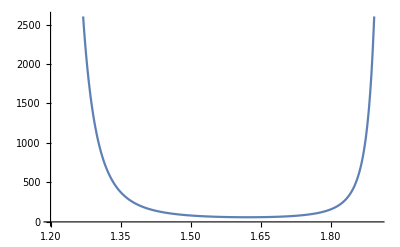

```mathematica
Plot[ⅇ^((Log[-1+b]-Log[b])/(2-3 b+b^2)),{b,1.2,1.9}]
```

```mathematica
FullSimplify[1/4 (-1+b) (2 y^((-1+b) b)-(-1+b) y^(-2+2 b))/.y->ⅇ^((Log[-1+b]-Log[b])/(2-3 b+b^2)),Assumptions->{1<b<2}]
```

1/4 (-(-1+b) ((-1+b)/b)^(2/(-2+b))+2 ((-1+b)/b)^(b/(-2+b))) (-1+b)

```mathematica
Limit[1/4 (-(-1+b) ((-1+b)/b)^(2/(-2+b))+2 ((-1+b)/b)^(b/(-2+b))) (-1+b),b->1]
```

1/4

```mathematica
Limit[1/4 (-(-1+b) ((-1+b)/b)^(2/(-2+b))+2 ((-1+b)/b)^(b/(-2+b))) (-1+b),b->1]
```

1/4

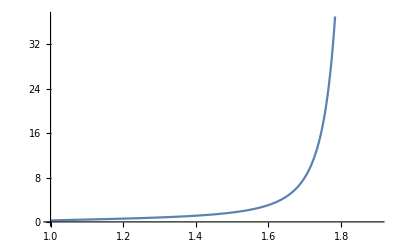

```mathematica
Plot[1/4 (-(-1+b) ((-1+b)/b)^(2/(-2+b))+2 ((-1+b)/b)^(b/(-2+b))) (-1+b),{b,1,1.9}]
```

```mathematica
FullSimplify[1/4 (-1+b) (2 y^((-1+b) b)-(-1+b) y^(-2+2 b))/.{y->ⅇ^((ⅈ π+Log[-1+1/b])/(2-3 b+b^2))},Assumptions->1<b<2]
```

```mathematica
1/4 (-1+b) (-(-1+b) (ⅇ^((ⅈ π+Log[-1+1/b])/(2-3 b+b^2)))^(2 (-1+b))+2 (ⅇ^((ⅈ π+Log[-1+1/b])/(2-3 b+b^2)))^((-1+b) b))/.b->3/2//N
```

1.6875-2.36658×10^-30 ⅈ

```mathematica
Integrate[t^(-d/2)Exp[ -r^2/(2t)+r^b] r^(d-1),{r,0,∞},Assumptions->{d≥1,t>0,b>0}]
```

Integrate[ⅇ^(r^b-r^2/(2 t)) r^(-1+d) t^(-d/2),{r,0,∞},Assumptions→{d≥1,t>0,b>0}]

```mathematica
D[r^b-(y-r)^2,r]
Solve[%==0,r]
```

b r^(-1+b)+2 (-r+y)

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[b r^(-1+b)+2 (-r+y)==0,r]

```mathematica
Integrate[Exp[-y^2+r^b-(r-y)^b],{y,0,r},Assumptions->{r>0,1<b<2}]
```

Integrate[ⅇ^(r^b-(r-y)^b-y^2),{y,0,r},Assumptions→{r>0,1<b<2}]

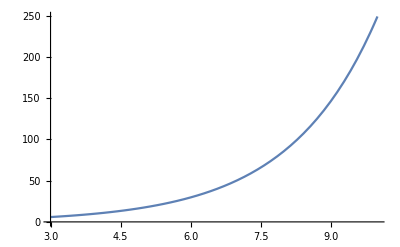

```mathematica
Plot[NIntegrate[Exp[-y^2+r^b-(r-y)^b]/.b->3/2,{y,0,r}],{r,3,10}]
```

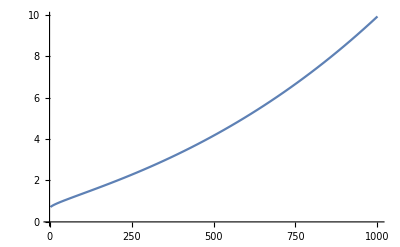

```mathematica
Plot[NIntegrate[Exp[-y^2+r^b-r^(b-1)-(r-y)^b]/.b->6/5,{y,0,r}],{r,3,1000}]
```

```mathematica
D[Integrate[Exp[-y^2+r^b-(r-y)^b],{y,0,r}],r]//FullSimplify
```

ⅇ^(-0^b-r^2+r^b)+∫_0^r b ⅇ^(r^b-(r-y)^b-y^2) (r^(-1+b)-(r-y)^(-1+b))ⅆy

```mathematica
D[Integrate[Exp[-y^2+r^b-(r-y)^b],{y,0,1}],r]//FullSimplify
```

∫_0^1 b ⅇ^(r^b-(r-y)^b-y^2) (r^(-1+b)-(r-y)^(-1+b))ⅆy

```mathematica
Series[(1+x)^(1/3),{x,0,3}]
```

1+x/3-x^2/9+(5 x^3)/81+O[x]^4

```mathematica
Series[(1+x)^(b-1),{x,0,3},Assumptions->{1<b≤2}]
```

1+(-1+b) x+1/2 (-2+b) (-1+b) x^2+1/6 (-3+b) (-2+b) (-1+b) x^3+O[x]^4

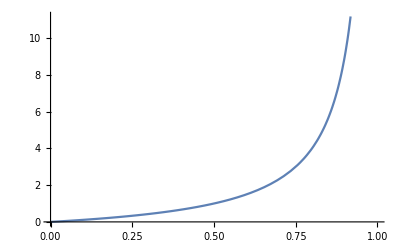

```mathematica
Plot[y/(1-y),{y,0,1}]
```

```mathematica
D[Integrate[Exp[-y^2+r^b-(r-y)^b],{y,0,r}],{r,2}]//FullSimplify
```

(ⅇ^(-0^b-r^2+r^b) (2 b r^b-r (0^(-1+b) b+2 r)))/r+ⅇ^(0^(1+b)) ∫_0^r ⅇ^(r^b-(r-y)^b-y^2) ((-1+b) b r^(-2+b)+(b r^(-1+b)-b (r-y)^(-1+b))^2-(-1+b) b (r-y)^(-2+b))ⅆy

```mathematica
FullSimplify[D[Integrate[Exp[-y^2+r^b-(r-y)^b],{y,0,r}],{r,2}],Assumptions->{1<b<2}]
```

-(2 ⅇ^(-r^2+r^b) (r^2-b r^b))/r+∫_0^r ⅇ^(r^b-(r-y)^b-y^2) ((-1+b) b r^(-2+b)+(b r^(-1+b)-b (r-y)^(-1+b))^2-(-1+b) b (r-y)^(-2+b))ⅆy

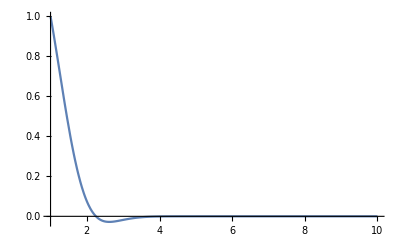

```mathematica
Plot[-(2 ⅇ^(-r^2+r^b) (r^2-b r^b))/r/.b->3/2,{r,1,10},PlotRange->Full]
```

```mathematica
Plot[((-1+b) b r^(-2+b)+(b r^(-1+b)-b (r-y)^(-1+b))^2-(-1+b) b (r-y)^(-2+b))/.b->3/2,{r,1,10},PlotRange->Full]
```

-Graphics-

```mathematica
-(2 ⅇ^(-r^2+r^b) (r^2-b r^b))/r+∫_0^r ⅇ^(r^b-(r-y)^b-y^2) ((-1+b) b r^(-2+b)+(b r^(-1+b)-b (r-y)^(-1+b))^2-(-1+b) b (r-y)^(-2+b))ⅆy/.b->3/2
```

-(2 ⅇ^(r^(3/2)-r^2) (-(3 r^(3/2))/2+r^2))/r+∫_0^r ⅇ^(r^(3/2)-(r-y)^(3/2)-y^2) (3/(4 √r)+((3 √r)/2-(3 √(r-y))/2)^2-3/(4 √(r-y)))ⅆy

```mathematica
(3/(4 √r)+((3 √r)/2-(3 √(r-r/3))/2)^2-3/(4 √(r-2r/3)))//FullSimplify
```

-(3 (-1+√3+(-5+2 √6) r^(3/2)))/(4 √r)

```mathematica
Limit[-(3 (-1+√3+(-5+2 √6) r^(3/2)))/(4 √r),r->∞]
```

```mathematica
Out[17]=
```

∞

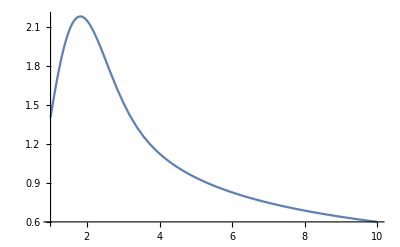

```mathematica
Plot[NIntegrate[Exp[-y^2+y^b] y/(r-y)^(2-b)/.b->3/2,{y,0,r}],{r,1,10}]
```

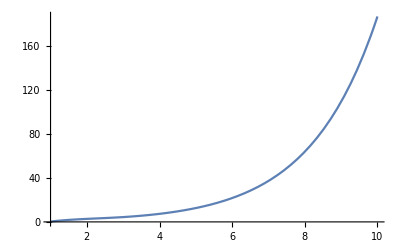

```mathematica
Plot[NIntegrate[Exp[-y^2+r^b-(r-y)^b]  y/(r-y)^(2-b)/.b->3/2,{y,1,r}],{r,1,10}]
```

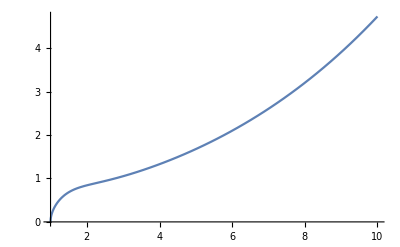

```mathematica
Plot[NIntegrate[Exp[-y^2+r^b-(r-1)^b]  1/(r-1)^(2-b)/.b->3/2,{y,1,r}],{r,1,10}]
```

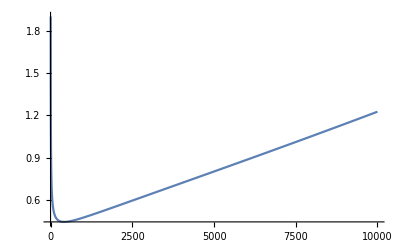

```mathematica
Plot[Exp[r^b-(r-1)^b]/(r-1)^(2-b)/.b->6/5,{r,0,10000}]
```

```mathematica
-r^2 + r^b - 2^(b/2-1)(r/2)^b//FullSimplify
```

```mathematica
-r^2+(1-2^(-1-b/2)) r^k
```

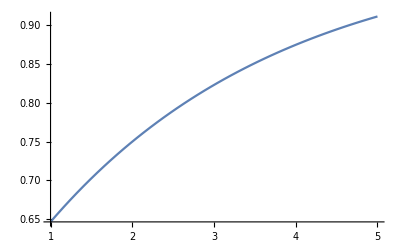

```mathematica
Plot[1-2^(-1-b/2),{b,1,5}]
```

```mathematica
Solve[1-2^(-1-b/2) == 0,b]
```

{{b→ConditionalExpression[2 (-1+(2 ⅈ π C[1])/Log[2]), C[1]∈ℤ]}}

```mathematica
Integrate[2  r^(d-1-2(1-α)) - r^(d-2(1-α)),{r,0,2},Assumptions->{d>=3}]
```

ConditionalExpression[2^(-1+d+2 α)/((-2+d+2 α) (-1+d+2 α)), d+2 Re[α]>2]

```mathematica
Integrate[(2π)^-d  (2 π^(d/2))/Gamma[d/2]  (2-r)r^(d-1-2(1-α)) ,{r,0,2},Assumptions->{d>=3,α>0}]//FullSimplify
```

```mathematica
(4^α π^(-d/2))/((-2+d+2 α) (-1+d+2 α) Gamma[d/2])//TeXForm
```

\frac{4^{\alpha } \pi
   ^{-d/2}}{(2 \alpha +d-2) (2
   \alpha +d-1) \Gamma
   \left(\frac{d}{2}\right)}

```mathematica
Integrate[(2π)^-d  (2 π^(d/2))/Gamma[d/2]  (2-r)r^(d-1-2(1-α)) ,{r,0,2},Assumptions->{d>=3,α>0}]/.d->1//FullSimplify
```

-2^(-1+2 α)/(π α-2 π α^2)

```mathematica
Integrate[(2π)^-d  (2 π^(d/2))/Gamma[d/2]  (2-r)r^(d-1-2(1-α)) ,{r,0,2},Assumptions->{d>=3,α>0}]/.d->3//FullSimplify
```

4^α/(π^2 (1+3 α+2 α^2))

```mathematica
Integrate[(2π)^-d  (2 π^(d/2))/Gamma[d/2]  (2-r)r^(d-1-2(1-α)) ,{r,0,2},Assumptions->{d>=3,α>0}]/.d->2//FullSimplify
```

2^(-1+2 α)/(π α+2 π α^2)